#### Function to convert hex to binary list

```mathematica
hStatetobState::state0="Blank (0) state given as argument";
hStatetobState::LastDigitErr="Last character of string was `1`, not 1, 2, 3, or 4";

hStatetobState[state_?(StringQ[#]||PossibleZeroQ[#]&)]:=
(* Takes a string that is an ALEKS knowledge state, and returns a list of binary digits, one for each item. 
The first input character should be an "x" to indicate it is in hex, 
and the last character says how many of the preceding characters 
are meaningful in the binary expansion. A "1" is added to keep all the previously leading 0s, but then the first character is 
dropped. 
This does not handle anything to do with differing domains. *)
If[state==0,
Message[hStatetobState::state0],
Module[{
last=StringTake[state,-1],
first=StringTake[state,1],
rest=StringTake[state,{2,-2}]},
If[first=="b",
state,
If[Not[MemberQ[{"1","2","3","4"},last]],
Message[hStatetobState::LastDigitErr,last];$Failed,
If[first=="x",
IntegerDigits[
FromDigits["1"<>rest,16],
2][[2;;ToExpression[last]-5]]
]]]]]
```

#### Directory on Washington

```mathematica
SetDirectory["~/TaR_grades/combined"];
```

#### Directory on MBP

```mathematica
SetDirectory["~/Google Drive/BU/TFing/TaR/"];
```

#### Import and format data

```mathematica
ch10914=Import["14CH109.csv","CSV"];
```

```mathematica
hstateGradeToBstateGrade[entry_List]:=
{hStatetobState[StringTake[entry[[1]],{1,-3}]],entry[[2]]}
```

```mathematica
formattedch10914=hstateGradeToBstateGrade/@ch10914;
```

```mathematica
ch10914X=formattedch10914[[All,1]];
ch10914y=formattedch10914[[All,2]];
```

#### Straight linear fit to all data

```mathematica
linCH10914=LinearModelFit[{ch10914X,ch10914y}]
```

FittedModel[0.-0.223218 #2+1.30728 #3+«475»+1.2935 #462]

#### Find how many no one knows and everyone knows

No student knows

```mathematica
Count[Or[##]&@@#&/@Transpose[ch10914X/.{0->False,1->True}],True]
```

272

Every student knows

```mathematica
Count[And[##]&@@#&/@Transpose[ch10914X/.{0->False,1->True}],True]
```

17

#### Fit to the total number of items known

```mathematica
totes=Total@Transpose[ch10914X];
```

```mathematica
lintot=LinearModelFit[Transpose[{totes,ch10914y}],x,x]
```

FittedModel[1.76615+0.010509 x]

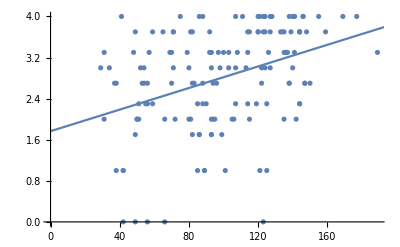

```mathematica
Show[ListPlot[Transpose[{totes,ch10914y}]],Plot[lintot[x],{x,0,200}]]
```

#### Split by “topic”

```mathematica
newSubjectIndices={1,44,72,83,164,199,207,247,266,267,289,296,308,326,351,355,359,364,379,407,449(* 462 total *)};
newSubjectIndices2=(newSubjectIndices[[2;;]]~Join~{463})-1;
```

```mathematica
topicSets=MapThread[Range,{newSubjectIndices,newSubjectIndices2}];
```

If there are fewer than 50 “True” items in any set, don’t try to do the fit. Instead, return a function that returns -1 for any non-empty argument sequence (this is helpful for ordering the fits later without disturbing the ordering and such).

```mathematica
topicFits=Block[{data=ch10914X[[All,#]]},If[Total[data,2]<50,Function[##;-1],LinearModelFit[{data,ch10914y}]]]&/@topicSets;
```

See if anything well describes, easily, data that will get a poor fit

```mathematica
N@Block[{data=ch10914X[[All,#]]},StandardDeviation@Flatten@data]&/@topicSets
N@Block[{data=ch10914X[[All,#]]},Total[data,2]]&/@topicSets
N@Block[{data=ch10914X[[All,#]]},Mean@Flatten@data]&/@topicSets
```

{0.0750047,0.376844,0.104599,0.466651,0.358988,0.393823,0.0183788,0.300905,0.302818,0.,0.498594,0.,0.0193746,0.046455,0.422096,0.423168,0.49783,0.0519289,0.458921,0.172153,0.46602}

{36.,3434.,1610.,3841.,787.,227.,2.,283.,133.,0.,476.,0.,1.,8.,137.,454.,407.,6.,1249.,190.,1412.}

{0.00565682,0.828668,0.988943,0.320404,0.151931,0.191723,0.000337838,0.10064,0.898649,0.,0.459459,0.,0.000375375,0.00216216,0.231419,0.766892,0.55,0.0027027,0.3014,0.0305663,0.681467}

```mathematica
splitARS=#["AdjustedRSquared"]&/@topicFits/.Missing[]->-1
splitRS=#["RSquared"]&/@topicFits/.Missing[]->-1
```

FittedModel::bdfit: The sum of squared errors is not a non-negative number. The model may suffer from significant numerical error or may not be appropriate for the data.

General::stop: Further output of FittedModel::bdfit will be suppressed during this calculation.

{-1,-0.011367,-0.0535152,-0.181872,-1,-1,-1,-1,0.818417,-1,0.752992,-1,-1,-1,0.706455,0.889882,0.804527,-1,-0.107175,-1,0.882901}

FittedModel::bdfit: The sum of squared errors is not a non-negative number. The model may suffer from significant numerical error or may not be appropriate for the data.

General::stop: Further output of FittedModel::bdfit will be suppressed during this calculation.

{-1,0.174394,0.0181525,0.461324,-1,-1,-1,-1,0.819644,-1,0.764675,-1,-1,-1,0.714389,0.892858,0.811131,-1,0.0961834,-1,0.893978}

#### Combine “well fit” pieces to see if them combined fits better

Find well-fit-sets (wfs) where the adjusted R^2 > 0.75

```mathematica
wfsIndices=Flatten@Position[splitARS,x_/;x>0.75];
```

```mathematica
wfs=Flatten@sets[[wfsIndices]];
```

Pull the data into a design matrix

```mathematica
wfsX=ch10914X[[All,wfs]];
```

Do the fit

```mathematica
wfsFit=LinearModelFit[{wfsX,ch10914y}]
```

FittedModel[0.684898 #1+0.494599 #2+«40»+0.367305 #30+0.399104 #31]

```mathematica
wfsFit["RSquared"]
wfsFit["AdjustedRSquared"]
```

0.920743

0.899743

#### Find optimal number of good sets of topics

```mathematica
Sort[splitARS,Greater]
```

{0.889882,0.882901,0.818417,0.804527,0.752992,0.706455,-0.011367,-0.0535152,-0.107175,-0.181872,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
tsOrder=Ordering[splitARS,All,Greater]
```

{16,21,9,17,11,15,2,3,19,4,20,18,14,13,12,10,8,7,6,5,1}

```mathematica
tsOrderedSets=Flatten/@(topicSets[[##]]&/@(tsOrder[[##]]&/@Range[Range[5]]));
```

```mathematica
tsOrderedFits=Block[{data=ch10914X[[All,#]]},
LinearModelFit[{data,ch10914y}]]&/@tsOrderedSets
```

LinearModelFit::rank: The rank of the design matrix 17 is less than the number of terms 18 in the model. The model and results based upon it may contain significant numerical error.

LinearModelFit::rank: The rank of the design matrix 18 is less than the number of terms 19 in the model. The model and results based upon it may contain significant numerical error.

LinearModelFit::rank: The rank of the design matrix 23 is less than the number of terms 24 in the model. The model and results based upon it may contain significant numerical error.

General::stop: Further output of LinearModelFit::rank will be suppressed during this calculation.

{FittedModel[-0.148417 #1+2.36667 #2+0.546667 #3+0.0506011 #4],FittedModel[-0.0641599 #1+1.5204 #2+«18»+0.636108 #16+0.407108 #17+0.538399 #18],FittedModel[-0.0683819 #1+1.42851 #2+«19»+0.390541 #17+0.507642 #18+0.673394 #19],FittedModel[-0.0597151 #1+1.53274 #2+«26»+0.422247 #22-0.120466 #23+0.396109 #24],FittedModel[-0.0426669 #1+1.68718 #2+«39»+0.326696 #30+0.323464 #31]}

```mathematica
Block[{data=ch10914X[[All,#]]},
MatrixRank[data]]&/@tsOrderedSets
```

{4,17,18,23,30}

```mathematica
tsOrderedARS=#["AdjustedRSquared"]&/@tsOrderedFits/.Missing[]->-1
tsOrderedRS=#["RSquared"]&/@tsOrderedFits/.Missing[]->-1
```

{0.889882,0.897812,0.899604,0.899852,0.899743}

{0.892858,0.910241,0.912493,0.916092,0.920743}

Seems that the first 4 is the optimal number in terms of Adjusted R^2, though the improvement is fairly minimal.
Also, based on the errors of low matrix rank, I’m guessing there are just some empty columns that should be excluded.

#### Fit to the sums of each topic

Test how to sum each topic

```mathematica
Total[ch10914X[[1;;2,#]]&/@sets,{3}]ᵀ
```

{{0,22,11,26,4,2,0,1,1,0,4,0,0,0,1,3,4,0,12,1,11},{0,27,11,37,12,1,0,0,1,0,4,0,0,0,1,4,4,0,11,1,10}}

Sum each topic. Also, form matrix with a 1 on the left for a constant bias term (y-intercept like terms).

```mathematica
splitTotals=Transpose[Total[ch10914X[[All,#]]&/@sets,{3}]];
splitTotalswConst=ArrayPad[splitTotals,{{0,0},{1,0}},1];
```

Do the fit

```mathematica
linSplitTotals=LinearModelFit[{splitTotals,ch10914y}]
linSplitTotalswConst=LinearModelFit[{splitTotalswConst,ch10914y}]
```

FittedModel[0.0659622 #1-0.120668 #2+«19» #3+«21»+«21» #19-0.0878084 #20-0.0685285 #21]

FittedModel[2.30858 #1+0.0644694 #2-«20» #3+«22»+«21» #20-0.0874663 #21-0.0624802 #22]

See that fit is quite inadequate

```mathematica
linSplitTotals["RSquared"]
linSplitTotals["AdjustedRSquared"]
linSplitTotalswConst["RSquared"]
linSplitTotalswConst["AdjustedRSquared"]
```

0.273193

0.158735

0.277927

0.157581